```mathematica
<<IGraphM`
```

IGraph/M 0.3.97.2 (February 5, 2018)

Evaluate IGDocumentation[] to get started.

```mathematica
Clear[latticer]

latticer[n_, r_]:=
(* Created a 1D periodic lattice with radius r *)
IGMakeLattice[{n},Radius ->r,Periodic->True]
```

```mathematica
Clear[setVertexProp]

setVertexProp[g_,prop_,vals_]:=
(*
	Sets the property prop of the vertices in g to vals;

	input;
		g: graph;
		prop: property of vertex;
		vals: a list of values;

	output;
		a graph
*)
Module[
{h=g,vl=VertexList@g},
Do[
PropertyValue[
{
h,
vl[[i]]
},
prop
]=vals[[i]],
{i,Length@vl}
];
Return@h]
```

```mathematica
Clear[grapherSi]

grapherSi[n_, k_, e_,si_] :=
(*
	Creates a graph of n members with random states (0/1);
	linked to their k nearest neighbors;
	The links are then each rewired with probability e;

	input;
		n: number of members;
		k: degrees of vertex;
		e: probablity of rewiring;

	outputs;
		a graph
*)

Module[
{r, states, graph,g1},

r = (* radius of lattice *)
Round[k/2];

states = (* a list of random states between 0 <-> 1 *)
RandomSample[
Join[
Table[0, si],
Table[1, n-si]]];

graph=  

setVertexProp[ (* sets the "State"s and VertexLabels to 'states' *)

IGRewireEdges[ (* rewires the graph with probability e *)
latticer[n,r],(* creates a graph of n members with radius r *)
e
],  

{"State", VertexLabels}, 
states

]
]
```

```mathematica
Clear[stringer]

stringer[i_] := "ab"<>ToString[i] (* creates a value "abi" for dummy variables in majority *)
```

```mathematica
Clear[majority]

majority[h_, list_] :=
True /; (Length[list ] == 2) ∧ (list[[1]] == list[[2]])

majority[h_, list_] :=
False /; (Length[list] == 2) ∧ !(list[[1]] == list[[2]])

majority[ h_, list_]:= 
(*
	Returns True if a majority above the threshold 'h' is reached in list;
	Returns False if no majority above the threshold 'h' is reached in list;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{
ab, swaps
},

ab = Table[stringer[i], {i, 1, Length[list]}];  (* dummy list of {ab1, ab2, ab3, ..., abN} where N is the length of list *)
swaps =  Dispatch[Table[ab[[i]] -> list[[i]], {i, 1, Length[list]}]]; (* creates a list of transformations {ab1 -> list[1], ab2 -> list[2], ..., abN -> list[N]} to swap back after BooleanCountingFunction *)

BooleanConvert[
(* converts from a functional form to disjunctive normal form *)
BooleanCountingFunction[
(* compares elements in list (element1 ∧ element2, ∧ is later swapped with ==) and returns True if at least a majority above the threshold h are agree  *)
{
Ceiling[h Length[list]],
Length[list]
},
Length[list]
] @@ ab

] //. swaps //. And -> Equal
]
```

```mathematica
Clear[newState]

newState[v_,h_, list_] :=
0 /;( majority[h,list] ∧ (Commonest[list][[1]] == 0))

newState[v_,h_,list_] :=
1 /; (majority[h, list] ∧ (Commonest[list][[1]] == 1))

newState[v_, h_, list_] := 
v /; !majority[h, list]

newState[v_,h_,list_] := 
list[[1]] /; Length[list] == 1
```

```mathematica
Clear[seter]

SetAttributes[seter, HoldFirst];

seter[g_,key_,value_,h_] :=
Module[
{
s, properties
},

s = PropertyValue[{g, key},"State"];
properties = PropertyValue[{g, #}, "State"] &/@ value;

PropertyValue[{g,key}, "State"] = newState[s, h, properties]]
```

```mathematica
Clear[propertyChanger]

SetAttributes[propertyChanger, HoldFirst];

propertyChanger[graph_, l_, h_] :=
MapThread[
seter[graph,#1,#2,0.6] &,{Keys[l], Values[l]}]
```

```mathematica
Clear[associatedAdjacencyLister]

associatedAdjacencyLister[g_] :=
(* 
Creates an association of vertices with vertices they are connected to;
(ie if vertex 1 is connected to {2,3,4} it would return <|1 -> {2,3,4},...|>);
*)
AssociationThread[
Range[1, Length[VertexList[g]]],
AdjacencyList[g,#] & /@ VertexList[g]]
```

```mathematica
Clear[iterator]

SetAttributes[iterator, HoldFirst];

iterator[g_, h_] := 
Module[
{propertyList},
propertyList =RandomSample[associatedAdjacencyLister[g]];

propertyChanger[g, propertyList, h]
]
```

```mathematica
Clear[modelerSi]

modelerSi[n_, {k_, h_, e_}, i_, si_] := 
(* 
	Implementation of Parkinson's Law  for decision-making in committees;
	

	inputs:
;	
		n: committee size (n ∈ ℕ);

		{k, h, e}: model parameters;
			k: connectivity (number of undirected links between nodes) (k ∈ ℕ);
			h: threshold (h ∈ [0.5, 1]);
			e: rewiring probability (e ∈ [0, 1]);

		i: iterations;


	outputs:
;
		graph probably
*)

Module[
{graph,o,states, plot},
graph = grapherSi[n, k, e,si];
states = {Table[PropertyValue[{graph, o}, "State"], {o, 1, n}]};

(*CellPrint@ExpressionCell[graph, "Output"];*)

Do[
iterator[graph,h]; 
AppendTo[states, Table[PropertyValue[{graph, o}, "State"], {o, 1, n}]], 
i
];

plot = ArrayPlot[states, Mesh->True];

{states, graph}
(*setVertexProp[ (* sets the "State"s and VertexLabels to 'states' *)

graph,
VertexLabels, 
Table[PropertyValue[{graph,o}, "State"], {o, 1, n}]

]
*)
(*CellPrint@ExpressionCell[#,"Output"]&/@{plot, graph}*)
]
```

```mathematica
Clear[finalState]

finalState[m_] := m[[1]][[-1]]
```

```mathematica
Clear[plotter]

plotter[m_] :=  (* Plots an array of the evolution of states *)
ArrayPlot[m[[1]], Mesh-> True]
```

```mathematica
Clear[grapher]

grapher[m_] :=m[[2]]
```

```mathematica
Clear[d]

d[n_, sf_] := 0 /; (n == sf)  ∨ (sf == 0)
d[n_, sf_] := 1 /; n ≠ sf
```

```mathematica
Clear[dissensus]

dissensus[n_, {k_, h_, e_}, i_]:=
Module[
{ms,fs,ds},
ms = Table[modelerSi[n, {k, h, e}, i, si], {si, 0, n}];

fs = finalState /@ ms;

ds = d[n, Count[#, 0]] & /@ fs;

Mean[ds]
]
```

```mathematica
Table[dissensus[4, {8, 0.8, 0.1}, 4], 10]
```

{0,0,0,0,0,0,0,0,0,0}

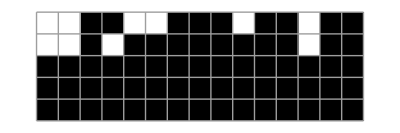

```mathematica
plotter[modelerSi[15, {8, 0.8, 0.1} ,4,6]]
```